```mathematica
raw=Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults.json"];
raw= Association[#]&/@raw;
```

```mathematica
raw[[1]]//Keys
```

{MTESet,solSet,P,norm_emit_x,norm_emit_y,emitSI90_x,emitSI90_y,sigmaSI90_x,sigmaSI90_y}

```mathematica
groupedData = GroupBy[raw,#MTESet&];
```

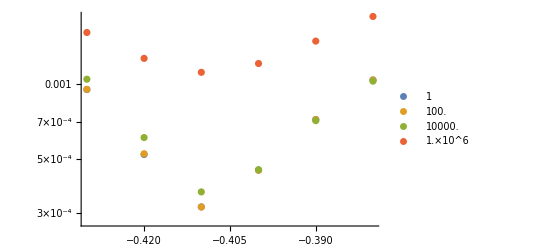

```mathematica
ListLogPlot[
Values[
{#["solSet"],#["sigmaSI90_x"]}&/@#&/@groupedData
],
PlotRange->All,
PlotLegends->Keys[groupedData]
]
```

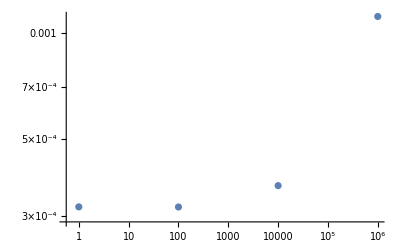

```mathematica
ListLogLogPlot[
{#MTESet,#["sigmaSI90_x"]}&/@Select[raw,#solSet == -0.41&]
]
```